```mathematica
{#,Style[5,FontFamily->#,Italic]}&/@Take[$FontFamilies]
```

```mathematica
Cambria
```

{0}

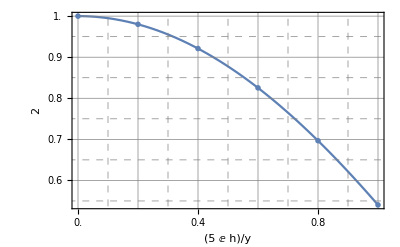

```mathematica
myplot[Plot][lable->{1,2,3,4}][Cos[x],{x,0,1},FrameLabel->{5 h/y E,2}]
```

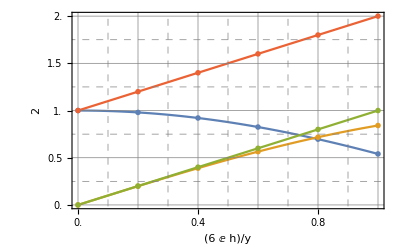

```mathematica
myplot[Plot][lable->{1,2,3,4}(*,LegendLayout->"Row"*)(*,PlotMarkers->{"α","β","γ","1"}*)][{Cos[x],Sin[x],x,x+1},{x,0,1},FrameLabel->{6 h/y E,2}]
```

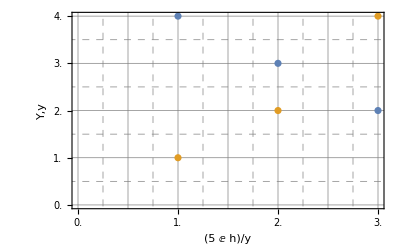

```mathematica
myplot[ListPlot][lable->{1,2,3,4}][{{4,3,2},{1,2,4}}]
```

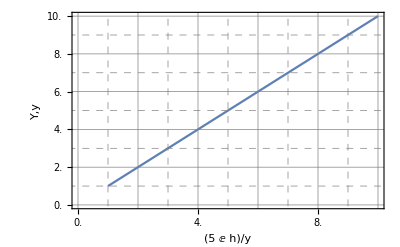

```mathematica
thelistlineplot[][Range[10]]
```

```mathematica
shadowbox[legend_]:=Graphics[{
Text[Framed[((*Print@#;*)#)&@legend/.Style[x_,xx___]:>Style[x,FontFamily->"Cambria",xx],Background->White,FrameMargins->0],{0.5,0.5},Center]
}]

myplot[Plot]:=theplot
myplot[ListPlot]:=thelistplot
myplot[ListLinePlot]:=thelistlineplot
theplot[x___][inf_?(Head[#]=!=List&),inrange_List,other___]:=theplot[x][{inf},inrange,other]
theplot[OptionsPattern[{lable->"Expressions",LegendLayout->"Column",PlotMarkers->"OpenMarkers"}]][inf_,inrange_List,other___]:=Block[{
range=<|1->{{0,1},{0,1}}|>,
plot=<|1->0|>,
ticks,
mesh
},
(*Print[OptionValue[PlotMarkers]];*)
(*基础作图,画图例,调用原本的plot*)
plot[1]=Plot[inf,inrange,PlotLegends->Placed[SwatchLegend[OptionValue[lable],LegendMarkers->"Line",LegendFunction->shadowbox,LegendLayout->OptionValue[LegendLayout]],{{0.7,0.9},{0.5,0.9}}]];
(*提取plot中的范围*)
range=MapIndexed[#2[[1]]->#1&,(PlotRange/.AbsoluteOptions[#,PlotRange])&/@Values[plot]]//Association;

(*刻度划分*)
ticks={({#,#,{0,.015}}&/@(N@FindDivisions[#[[1]],6])),({#,"",{0,.008}}&/@N@FindDivisions[#[[1]],30]),({#,#,{0,.015}}&/@(N@FindDivisions[#[[2]],5])),({#,"",{0,.008}}&/@N@FindDivisions[#[[2]],25])}&/@range;

(*标记点*)
mesh=ListPlot[Table[({x,#})&/@inf,{x,#[[1,;;,1]]}]//Transpose,PlotMarkers->OptionValue[PlotMarkers],PlotLegends->{x,y},PlotTheme->"Default"]&/@ticks;
(*Echo[mesh[1][[1,1]]]*);

(*综合设置*)
(plot[1]/.{
Graphics[graph_,s___]:>Graphics[{graph,mesh[1][[1,1]]},other,Frame->True,
FrameLabel->{5 h/y E,"Y,y"},

FrameStyle->Directive[Black],


FrameTicks->{{ticks[1][[3]]~Join~ticks[1][[4]],None},{ticks[1][[1]]~Join~ticks[1][[2]],None}},
BaseStyle->{Black,10,FontFamily->"Cambria"},
GridLines->{ticks[1][[1,;;,1]]~Join~(({#,Dashed})&/@MovingAverage[ticks[1][[1,;;,1]],2]),ticks[1][[3,;;,1]]~Join~(({#,Dashed})&/@MovingAverage[ticks[1][[3,;;,1]],2])},
GridLinesStyle->Directive[Gray],
s
]
(*,(LegendMarkers->x___)->Echo@(LegendMarkers->(*Graphics[{Echo@Inset[*){Cases[mesh[1],Rule[LegendMarkers,x___]->x,Infinity][[1]]}(*,{0.5,0.5},Center]}]*))*)

,(LegendMarkers->x___)->(LegendMarkers->(Cases[mesh[1],Rule[LegendMarkers,x___]->x,Infinity][[1]])/.Graphics[x_,y___]:>Graphics[(*Print[x//FullForm];*){Line[{Offset[{20,0}],Offset[{-20,0}]}]}~Join~x,y](*/. 9.75->20*))

})
]
thelistplot[x___][inf_?(Head[#]=!=List&),other___]:=thelistplot[x][{inf},other]
thelistplot[OptionsPattern[{lable->"Expressions",LegendLayout->"Column",PlotMarkers->"OpenMarkers"}]][inf_,other___]:=Block[{
range=<|1->{{0,1},{0,1}}|>,
plot=<|1->0|>,
ticks,
mesh
},
(*Print[OptionValue[PlotMarkers]];*)
(*基础作图,画图例,调用原本的plot*)
plot[1]=ListPlot[inf,PlotLegends->Placed[SwatchLegend[OptionValue[lable],LegendMarkers->"Line",LegendFunction->shadowbox,LegendLayout->OptionValue[LegendLayout]],{{0.7,0.9},{0.5,0.9}}]];
(*提取plot中的范围*)
range=MapIndexed[#2[[1]]->#1&,(PlotRange/.AbsoluteOptions[#,PlotRange])&/@Values[plot]]//Association;

(*刻度划分*)
ticks={({#,#,{0,.015}}&/@(N@FindDivisions[#[[1]],6])),({#,"",{0,.008}}&/@N@FindDivisions[#[[1]],30]),({#,#,{0,.015}}&/@(N@FindDivisions[#[[2]],5])),({#,"",{0,.008}}&/@N@FindDivisions[#[[2]],25])}&/@range;

(*标记点*)
mesh=ListPlot[inf,PlotMarkers->OptionValue[PlotMarkers],PlotLegends->{x,y},PlotTheme->"Default"]&/@ticks;
(*Echo[mesh[1][[1,1]]]*);

(*综合设置*)
(plot[1]/.{
Graphics[graph_,s___]:>Graphics[{graph(*,mesh[1][[1,1]]*)},other,Frame->True,
FrameLabel->{5 h/y E,"Y,y"},

FrameStyle->Directive[Black],


FrameTicks->{{ticks[1][[3]]~Join~ticks[1][[4]],None},{ticks[1][[1]]~Join~ticks[1][[2]],None}},
BaseStyle->{Black,10,FontFamily->"Cambria"},
GridLines->{ticks[1][[1,;;,1]]~Join~(({#,Dashed})&/@MovingAverage[ticks[1][[1,;;,1]],2]),ticks[1][[3,;;,1]]~Join~(({#,Dashed})&/@MovingAverage[ticks[1][[3,;;,1]],2])},
GridLinesStyle->Directive[Gray],
s
]
(*,(LegendMarkers->x___)->Echo@(LegendMarkers->(*Graphics[{Echo@Inset[*){Cases[mesh[1],Rule[LegendMarkers,x___]->x,Infinity][[1]]}(*,{0.5,0.5},Center]}]*))*)

,(LegendMarkers->x___)->(LegendMarkers->(Cases[mesh[1],Rule[LegendMarkers,x___]->x,Infinity][[1]])/.Graphics[x_,y___]:>Graphics[(*Print[x//FullForm];*){Line[{Offset[{20,0}],Offset[{-20,0}]}]}~Join~x,y](*/. 9.75->20*))

})
];
thelistlineplot[x___][inf_?(Head[#]=!=List&),other___]:=thelistlineplot[x][{inf},other]
thelistlineplot[OptionsPattern[{lable->"Expressions",LegendLayout->"Column",PlotMarkers->"OpenMarkers"}]][inf_,other___]:=Block[{
range=<|1->{{0,1},{0,1}}|>,
plot=<|1->0|>,
ticks,
mesh
},
(*Print[OptionValue[PlotMarkers]];*)
(*基础作图,画图例,调用原本的plot*)
plot[1]=ListLinePlot[inf,PlotLegends->Placed[SwatchLegend[OptionValue[lable],LegendMarkers->"Line",LegendFunction->shadowbox,LegendLayout->OptionValue[LegendLayout]],{{0.7,0.9},{0.5,0.9}}]];
(*提取plot中的范围*)
range=MapIndexed[#2[[1]]->#1&,(PlotRange/.AbsoluteOptions[#,PlotRange])&/@Values[plot]]//Association;

(*刻度划分*)
ticks={({#,#,{0,.015}}&/@(N@FindDivisions[#[[1]],6])),({#,"",{0,.008}}&/@N@FindDivisions[#[[1]],30]),({#,#,{0,.015}}&/@(N@FindDivisions[#[[2]],5])),({#,"",{0,.008}}&/@N@FindDivisions[#[[2]],25])}&/@range;

(*标记点*)
mesh=ListPlot[inf,PlotMarkers->OptionValue[PlotMarkers],PlotLegends->{x,y},PlotTheme->"Default"]&/@ticks;
(*Echo[mesh[1][[1,1]]]*);

(*综合设置*)
(plot[1]/.{
Graphics[graph_,s___]:>Graphics[{graph(*,mesh[1][[1,1]]*)},other,Frame->True,
FrameLabel->{5 h/y E,"Y,y"},

FrameStyle->Directive[Black],


FrameTicks->{{ticks[1][[3]]~Join~ticks[1][[4]],None},{ticks[1][[1]]~Join~ticks[1][[2]],None}},
BaseStyle->{Black,10,FontFamily->"Cambria"},
GridLines->{ticks[1][[1,;;,1]]~Join~(({#,Dashed})&/@MovingAverage[ticks[1][[1,;;,1]],2]),ticks[1][[3,;;,1]]~Join~(({#,Dashed})&/@MovingAverage[ticks[1][[3,;;,1]],2])},
GridLinesStyle->Directive[Gray],
s
]
(*,(LegendMarkers->x___)->Echo@(LegendMarkers->(*Graphics[{Echo@Inset[*){Cases[mesh[1],Rule[LegendMarkers,x___]->x,Infinity][[1]]}(*,{0.5,0.5},Center]}]*))*)

,(LegendMarkers->x___)->(LegendMarkers->(Cases[mesh[1],Rule[LegendMarkers,x___]->x,Infinity][[1]])/.Graphics[x_,y___]:>Graphics[(*Print[x//FullForm];*){Line[{Offset[{20,0}],Offset[{-20,0}]}]}~Join~x,y](*/. 9.75->20*))

})
]
```